Restoration Coefficient R = 0.577114

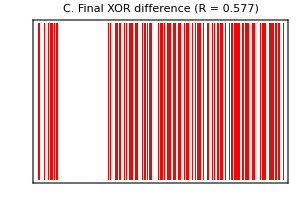

```mathematica
ClearAll["Global`*"];

(* =========================1. Parameters=========================*)
rule=30;
width=201;
steps=150;
injuryStep=40;
injuryRadius=8;

(* =========================2. Initial 1D mantle state=========================*)
init=ConstantArray[0,width];
init[[Ceiling[width/2]]]=1;

(* =========================3. Control evolution=========================*)
controlEvo=CellularAutomaton[rule,init,steps];

(* =========================4. Injure one intermediate row=========================*)
injuredState=controlEvo[[injuryStep+1]];

center=Ceiling[width/2];
injuryPositions=Range[center-injuryRadius,center+injuryRadius];

injuredState2=ReplacePart[injuredState,Thread[injuryPositions->RandomInteger[1,Length[injuryPositions]]]];

(* =========================5. Continue evolution after injury=========================*)
postInjuryEvo=CellularAutomaton[rule,injuredState2,steps-injuryStep];

injuredFullEvo=Join[controlEvo[[1;;injuryStep]],postInjuryEvo];

(* =========================6. Difference map and restoration coefficient=========================*)
finalControl=controlEvo[[-1]];
finalInjured=injuredFullEvo[[-1]];

xorFinal=Mod[finalControl+finalInjured,2];

R=1-N[Total[xorFinal]/Length[xorFinal]];

Print["Restoration Coefficient R = ",R];

(* =========================7. Visualization=========================*)
panel1=ArrayPlot[controlEvo,ColorRules->{0->White,1->Black},Frame->True,Mesh->False,PlotLabel->Style["A. Control Conus-like growth",13,Bold],ImageSize->300];

panel2=ArrayPlot[injuredFullEvo,ColorRules->{0->White,1->Black},Frame->True,Mesh->False,PlotLabel->Style["B. Injured Conus-like growth",13,Bold],ImageSize->300];

panel3=ArrayPlot[{xorFinal},ColorRules->{0->White,1->Red},Frame->True,Mesh->False,PlotLabel->Style["C. Final XOR difference (R = "<>ToString[NumberForm[R,{3,3}]]<>")",13,Bold],ImageSize->300];

GraphicsRow[{panel1,panel2,panel3},Spacings->20,ImageSize->1000]
```

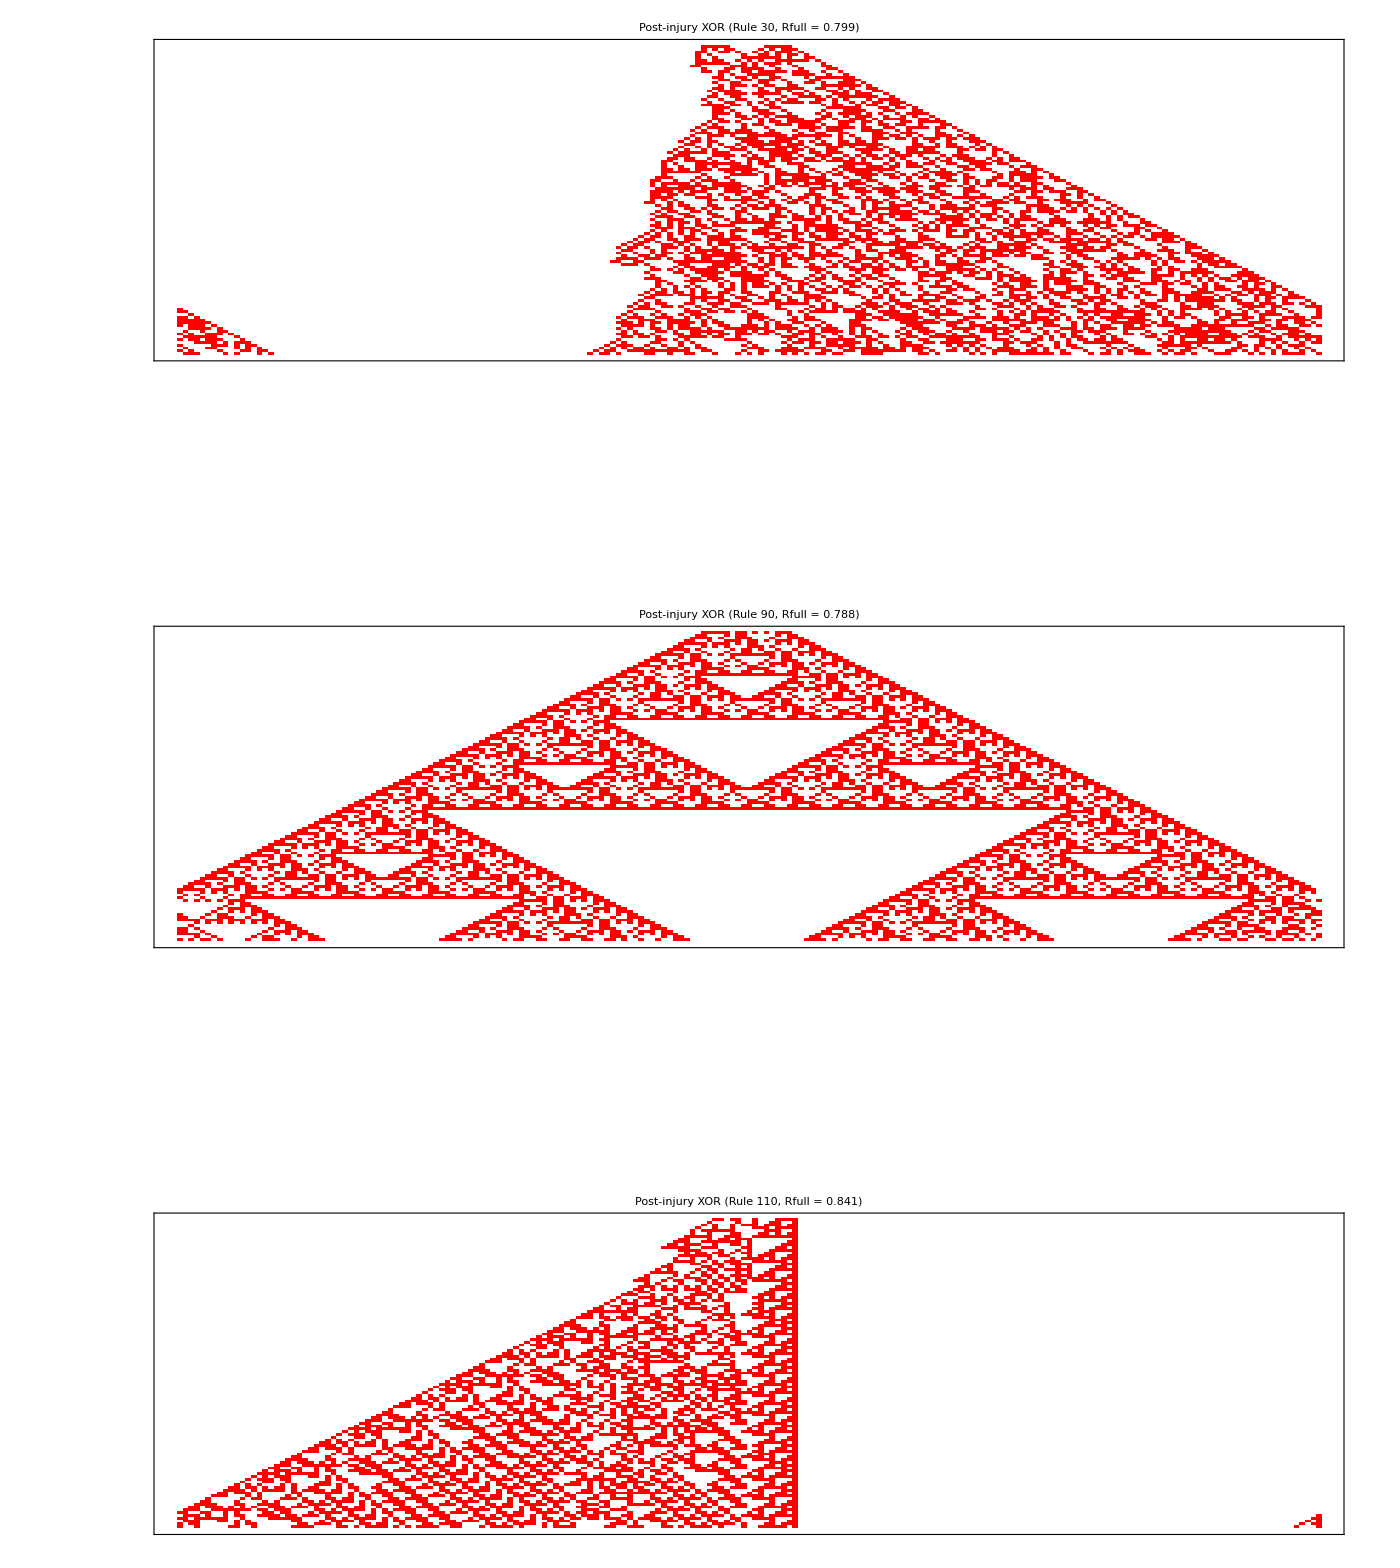

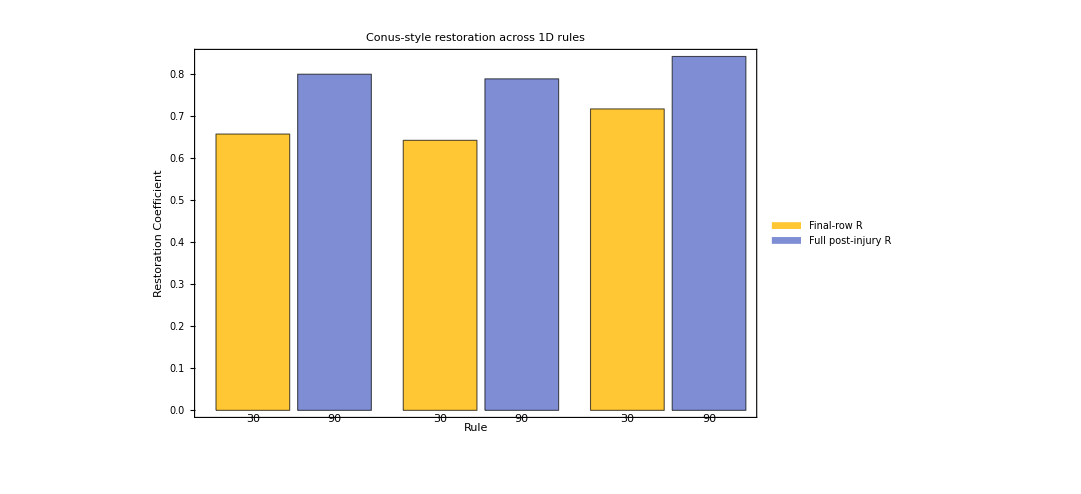

All exports saved in: /Volumes/External/Ruliology/conus_restoration_exports

```mathematica
ClearAll["Global`*"];

(* =========================================================1. USER PARAMETERS=========================================================*)

rulesToTest={30,90,110};
width=201;
steps=150;
injuryStep=40;
injuryRadius=8;
randomSeed=12345;

exportBase=FileNameJoin[{NotebookDirectory[],"conus_restoration_exports"}];

SeedRandom[randomSeed];

If[!DirectoryQ[exportBase],CreateDirectory[exportBase]];

(* =========================================================2. HELPERS=========================================================*)

makeInitialState[w_Integer]:=Module[{init},init=ConstantArray[0,w];
init[[Ceiling[w/2]]]=1;
init];

injureState[state_List,radius_Integer]:=Module[{center,injuryPositions,replacementValues},center=Ceiling[Length[state]/2];
injuryPositions=Select[Range[center-radius,center+radius],1<=#<=Length[state]&];
replacementValues=RandomInteger[1,Length[injuryPositions]];
ReplacePart[state,Thread[injuryPositions->replacementValues]]];

restorationMetrics[controlEvo_,injuredFullEvo_,injStep_Integer]:=Module[{finalControl,finalInjured,xorFinal,Rfinal,controlPost,injuredPost,xorPost,Rfull},finalControl=controlEvo[[-1]];
finalInjured=injuredFullEvo[[-1]];
xorFinal=Mod[finalControl+finalInjured,2];
Rfinal=1-N[Total[xorFinal]/Length[xorFinal]];
controlPost=controlEvo[[injStep+1;;]];
injuredPost=injuredFullEvo[[injStep+1;;]];
xorPost=Mod[controlPost+injuredPost,2];
Rfull=1-N[Total[Flatten[xorPost]]/Length[Flatten[xorPost]]];
<|"FinalXOR"->xorFinal,"PostXOR"->xorPost,"Rfinal"->Rfinal,"Rfull"->Rfull|>];

plotControl[evo_,rule_]:=ArrayPlot[evo,ColorRules->{0->White,1->Black},Frame->True,Mesh->False,PlotLabel->Style["A. Control growth (Rule "<>ToString[rule]<>")",13,Bold],ImageSize->320];

plotInjured[evo_,rule_,injStep_]:=Show[ArrayPlot[evo,ColorRules->{0->White,1->Black},Frame->True,Mesh->False,PlotLabel->Style["B. Injured growth (Rule "<>ToString[rule]<>")",13,Bold],ImageSize->320],Graphics[{{Red,Thick,Dashed,Line[{{0.5,injStep+1.5},{Length[evo[[1]]]+0.5,injStep+1.5}}]}}]];

plotFinalXOR[xorRow_,rVal_,rule_]:=ArrayPlot[{xorRow},ColorRules->{0->White,1->Red},Frame->True,Mesh->False,PlotLabel->Style["C. Final XOR (Rule "<>ToString[rule]<>", R = "<>ToString[NumberForm[rVal,{3,3}]]<>")",13,Bold],ImageSize->320];

plotPostXOR[xorPost_,rVal_,rule_]:=ArrayPlot[xorPost,ColorRules->{0->White,1->Red},Frame->True,Mesh->False,PlotLabel->Style["Post-injury XOR (Rule "<>ToString[rule]<>", Rfull = "<>ToString[NumberForm[rVal,{3,3}]]<>")",13,Bold],ImageSize->320];

exportGraphic[g_,path_]:=Export[path,g,ImageResolution->300];

(* =========================================================3. MAIN SIMULATION FUNCTION=========================================================*)

runConusRestoration[rule_Integer]:=Module[{init,controlEvo,injuredState,postInjuryEvo,injuredFullEvo,metrics,panelRow,xorPanel,resultDir,controlPlot,injuredPlot,finalXORPlot,postXORPlot},resultDir=FileNameJoin[{exportBase,"rule_"<>ToString[rule]}];
If[!DirectoryQ[resultDir],CreateDirectory[resultDir]];
init=makeInitialState[width];
controlEvo=CellularAutomaton[rule,init,steps];
injuredState=injureState[controlEvo[[injuryStep+1]],injuryRadius];
postInjuryEvo=CellularAutomaton[rule,injuredState,steps-injuryStep];
injuredFullEvo=Join[controlEvo[[1;;injuryStep]],postInjuryEvo];
metrics=restorationMetrics[controlEvo,injuredFullEvo,injuryStep];
controlPlot=plotControl[controlEvo,rule];
injuredPlot=plotInjured[injuredFullEvo,rule,injuryStep];
finalXORPlot=plotFinalXOR[metrics["FinalXOR"],metrics["Rfinal"],rule];
postXORPlot=plotPostXOR[metrics["PostXOR"],metrics["Rfull"],rule];
panelRow=GraphicsRow[{controlPlot,injuredPlot,finalXORPlot},Spacings->20,ImageSize->1100];
xorPanel=postXORPlot;
exportGraphic[controlPlot,FileNameJoin[{resultDir,"control.png"}]];
exportGraphic[injuredPlot,FileNameJoin[{resultDir,"injured.png"}]];
exportGraphic[finalXORPlot,FileNameJoin[{resultDir,"final_xor.png"}]];
exportGraphic[xorPanel,FileNameJoin[{resultDir,"postinjury_xor.png"}]];
exportGraphic[panelRow,FileNameJoin[{resultDir,"three_panel_summary.png"}]];
Export[FileNameJoin[{resultDir,"three_panel_summary.pdf"}],panelRow];
Export[FileNameJoin[{resultDir,"postinjury_xor.pdf"}],xorPanel];
<|"Rule"->rule,"ControlEvolution"->controlEvo,"InjuredEvolution"->injuredFullEvo,"FinalXOR"->metrics["FinalXOR"],"PostXOR"->metrics["PostXOR"],"Rfinal"->metrics["Rfinal"],"Rfull"->metrics["Rfull"],"ThreePanelGraphic"->panelRow,"PostXORGraphic"->xorPanel|>];

(* =========================================================4. RUN ALL RULES=========================================================*)

results=runConusRestoration/@rulesToTest;

(* =========================================================5. SUMMARY TABLE=========================================================*)

summaryTable=Dataset[results/. assoc_Association:><|"Rule"->assoc["Rule"],"Final Restoration Coefficient"->NumberForm[assoc["Rfinal"],{4,3}],"Full Post-Injury Restoration Coefficient"->NumberForm[assoc["Rfull"],{4,3}],"Width"->width,"Steps"->steps,"Injury Step"->injuryStep,"Injury Radius"->injuryRadius|>];

summaryTable

Export[FileNameJoin[{exportBase,"conus_restoration_summary_table.csv"}],Prepend[(results/. assoc_Association:>{assoc["Rule"],assoc["Rfinal"],assoc["Rfull"],width,steps,injuryStep,injuryRadius}),{"Rule","FinalRestorationCoefficient","FullPostInjuryRestorationCoefficient","Width","Steps","InjuryStep","InjuryRadius"}]];

(* =========================================================6. COMBINED COMPARISON FIGURE=========================================================*)

comparisonFigure=GraphicsGrid[Partition[Flatten[({#[["ThreePanelGraphic"]],#[["PostXORGraphic"]]}&/@results)],2],Spacings->{0.8,1.0},ImageSize->1400];

comparisonFigure

Export[FileNameJoin[{exportBase,"conus_restoration_comparison.png"}],comparisonFigure,ImageResolution->300];

Export[FileNameJoin[{exportBase,"conus_restoration_comparison.pdf"}],comparisonFigure];

(* =========================================================7. OPTIONAL:BAR CHART OF RESTORATION COEFFICIENTS=========================================================*)

barChart=BarChart[{results[[All,"Rfinal"]],results[[All,"Rfull"]]}ᵀ,ChartLabels->Placed[ToString/@rulesToTest,Below],ChartLegends->{"Final-row R","Full post-injury R"},Frame->True,FrameLabel->{"Rule","Restoration Coefficient"},PlotLabel->Style["Conus-style restoration across 1D rules",14,Bold],ImageSize->800];

barChart

Export[FileNameJoin[{exportBase,"conus_restoration_barchart.png"}],barChart,ImageResolution->300];

Export[FileNameJoin[{exportBase,"conus_restoration_barchart.pdf"}],barChart];

(* =========================================================8. PRINT OUTPUT LOCATION=========================================================*)

Print["All exports saved in: ",exportBase];
```

```mathematica
ClearAll["Global`*"];

(* =========================================================1. PARAMETERS=========================================================*)

allRules=Range[0,255];
width=201;
steps=150;
injuryStep=40;
injuryRadius=8;
randomSeed=12345;

exportBase=FileNameJoin[{NotebookDirectory[],"wolfram_256_rule_scan"}];
SeedRandom[randomSeed];

If[!DirectoryQ[exportBase],CreateDirectory[exportBase]];

(* =========================================================2. HELPERS=========================================================*)

makeInitialState[w_Integer]:=Module[{init},init=ConstantArray[0,w];
init[[Ceiling[w/2]]]=1;
init];

injureState[state_List,radius_Integer]:=Module[{center,injuryPositions,replacementValues},center=Ceiling[Length[state]/2];
injuryPositions=Select[Range[center-radius,center+radius],1<=#<=Length[state]&];
replacementValues=RandomInteger[1,Length[injuryPositions]];
ReplacePart[state,Thread[injuryPositions->replacementValues]]];

restorationMetrics[controlEvo_,injuredFullEvo_,injStep_Integer]:=Module[{finalControl,finalInjured,xorFinal,Rfinal,controlPost,injuredPost,xorPost,Rfull},finalControl=controlEvo[[-1]];
finalInjured=injuredFullEvo[[-1]];
xorFinal=Mod[finalControl+finalInjured,2];
Rfinal=1-N[Total[xorFinal]/Length[xorFinal]];
controlPost=controlEvo[[injStep+1;;]];
injuredPost=injuredFullEvo[[injStep+1;;]];
xorPost=Mod[controlPost+injuredPost,2];
Rfull=1-N[Total[Flatten[xorPost]]/Length[Flatten[xorPost]]];
<|"FinalXOR"->xorFinal,"PostXOR"->xorPost,"Rfinal"->Rfinal,"Rfull"->Rfull|>];

patternDensity[evo_]:=N[Mean[Flatten[evo]]];

rowEntropy[row_List]:=Module[{p},p=N[Counts[row]/Length[row]];
-Total[Values[p]*Log2[Values[p]+10^-12]]];

meanEntropy[evo_]:=Mean[rowEntropy/@evo];

(*crude activity metric:how much adjacent variation*)
adjacencyVariation[evo_]:=Mean[Flatten[Table[Mean[Boole[Differences[evo[[i]]]!=0]],{i,Length[evo]}]]];

classifyRule[evo_,rfull_,density_,entropy_,variation_]:=Which[density<0.02,"Trivial sparse",density>0.98,"Trivial full",entropy<0.15&&variation<0.05,"Simple periodic",entropy>0.8&&variation>0.45&&rfull<0.75,"Chaotic fragile",entropy>0.5&&variation>0.25&&rfull>=0.75,"Structured robust",variation>0.15&&variation<0.35,"Fractal / nested",True,"Mixed / intermediate"];

thumbnailPlot[evo_,rule_,rfull_]:=ArrayPlot[evo,ColorRules->{0->White,1->Black},Frame->True,Mesh->False,ImageSize->180,PlotLabel->Style["Rule "<>ToString[rule]<>"\nRfull = "<>ToString[NumberForm[rfull,{3,3}]],10,Bold]];

(* =========================================================3. SINGLE RULE ANALYSIS=========================================================*)

analyzeRule[rule_Integer]:=Module[{init,controlEvo,injuredState,postInjuryEvo,injuredFullEvo,metrics,density,entropy,variation,class,thumb},init=makeInitialState[width];
controlEvo=CellularAutomaton[rule,init,steps];
injuredState=injureState[controlEvo[[injuryStep+1]],injuryRadius];
postInjuryEvo=CellularAutomaton[rule,injuredState,steps-injuryStep];
injuredFullEvo=Join[controlEvo[[1;;injuryStep]],postInjuryEvo];
metrics=restorationMetrics[controlEvo,injuredFullEvo,injuryStep];
density=patternDensity[controlEvo];
entropy=meanEntropy[controlEvo];
variation=adjacencyVariation[controlEvo];
class=classifyRule[controlEvo,metrics["Rfull"],density,entropy,variation];
thumb=thumbnailPlot[controlEvo,rule,metrics["Rfull"]];
Export[FileNameJoin[{exportBase,"rule_"<>IntegerString[rule,10,3]<>".png"}],thumb,ImageResolution->200];
<|"Rule"->rule,"ControlEvolution"->controlEvo,"InjuredEvolution"->injuredFullEvo,"Rfinal"->metrics["Rfinal"],"Rfull"->metrics["Rfull"],"Density"->density,"Entropy"->entropy,"Variation"->variation,"Class"->class,"Thumbnail"->thumb|>];

(* =========================================================4. RUN ALL 256 RULES=========================================================*)

results256=analyzeRule/@allRules;

(* =========================================================5. EXPORT SUMMARY TABLE=========================================================*)

summaryRows=results256/. assoc_Association:>{assoc["Rule"],assoc["Rfinal"],assoc["Rfull"],assoc["Density"],assoc["Entropy"],assoc["Variation"],assoc["Class"]};

summaryHeader={"Rule","Rfinal","Rfull","Density","Entropy","Variation","Class"};

Export[FileNameJoin[{exportBase,"wolfram_256_summary.csv"}],Prepend[summaryRows,summaryHeader]];

summaryDataset=Dataset[results256/. assoc_Association:><|"Rule"->assoc["Rule"],"Rfinal"->NumberForm[assoc["Rfinal"],{4,3}],"Rfull"->NumberForm[assoc["Rfull"],{4,3}],"Density"->NumberForm[assoc["Density"],{4,3}],"Entropy"->NumberForm[assoc["Entropy"],{4,3}],"Variation"->NumberForm[assoc["Variation"],{4,3}],"Class"->assoc["Class"]|>];

summaryDataset
```

Dataset[<>]

```mathematica
topRobust=TakeLargestBy[results256,#["Rfull"]&,20];

Dataset[topRobust/. assoc_Association:><|"Rule"->assoc["Rule"],"Rfull"->NumberForm[assoc["Rfull"],{4,3}],"Class"->assoc["Class"],"Entropy"->NumberForm[assoc["Entropy"],{4,3}],"Variation"->NumberForm[assoc["Variation"],{4,3}]|>]
```

Dataset[<>]

```mathematica
interestingRules=Select[results256,(#["Rfull"]>0.70&&#["Entropy"]>0.20&&#["Variation"]>0.05&&#["Density"]>0.01&&#["Density"]<0.99)&];

Dataset[interestingRules/. assoc_Association:><|"Rule"->assoc["Rule"],"Rfull"->NumberForm[assoc["Rfull"],{4,3}],"Class"->assoc["Class"],"Entropy"->NumberForm[assoc["Entropy"],{4,3}],"Variation"->NumberForm[assoc["Variation"],{4,3}]|>]
```

```mathematica
thumbs=(#[["Thumbnail"]]&/@Take[interestingRules,UpTo[36]]);

contactSheet=GraphicsGrid[Partition[thumbs,UpTo[6]],Spacings->{0.4,0.6},ImageSize->1400];

contactSheet

Export[FileNameJoin[{exportBase,"interesting_rule_contact_sheet.png"}],contactSheet,ImageResolution->300];
```

GraphicsGrid::list: {} is not a list of lists.

GraphicsGrid[{},Spacings→{0.4,0.6},ImageSize→1400]

Show::gtype: GraphicsGrid is not a type of graphics.